```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
ys[x_]:={Cos[2 π x/L],Sin[2 π x /L]}
```

```mathematica
(*check for u[[1]]*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/first_order_pde/periodic/solution/nodal_values/ys.csv"][[2;;]];
t=Table[{t[[i,4]],t[[i,1]]},{i,2,Length[t]}]
```

{{0.9,0.809017},{0.8,0.309017},{0.7,-0.309017},{0.6,-0.809017},{0.5,-1.},{0.4,-0.809017},{0.3,-0.309017},{0.2,0.309017},{0.1,0.809017},{0.,1.}}

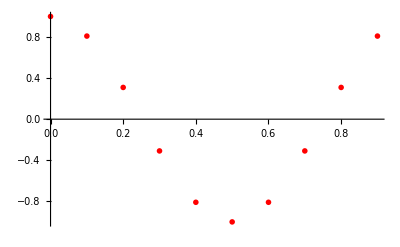

```mathematica
plotnum=ListPlot[t,PlotStyle->{Red,PointSize->0.01}]
```

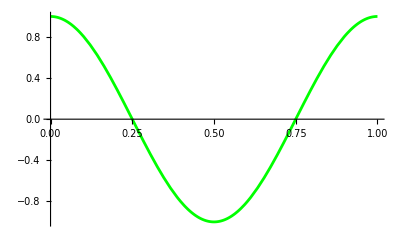

```mathematica
plotexact=Plot[ys[x][[1]],{x,0,L},PlotRange->Full,PlotStyle->Green]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-ys[t[[i,1]]][[1]]],{i,1,Length[t]}]]
```

1.11022×10^-16

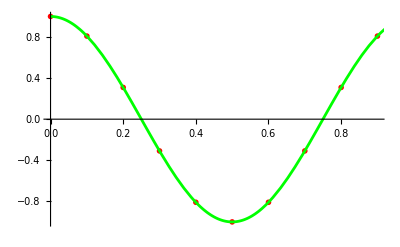

```mathematica
Show[plotnum,plotexact]
```

```mathematica
(*check for u[[2]]*)
```

```mathematica
t=Import["/Users/michelecastellana/Documents/finite_elements/first_order_pde/periodic/solution/nodal_values/ys.csv"][[2;;]];
t=Table[{t[[i,4]],t[[i,2]]},{i,2,Length[t]}]
```

{{0.9,-0.587785},{0.8,-0.951057},{0.7,-0.951057},{0.6,-0.587785},{0.5,1.40458×10^-16},{0.4,0.587785},{0.3,0.951057},{0.2,0.951057},{0.1,0.587785},{0.,5.16755×10^-17}}

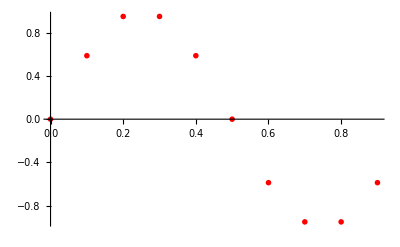

```mathematica
plotnum=ListPlot[t,PlotStyle->{Red,PointSize->0.01}]
```

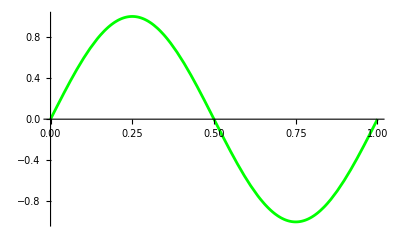

```mathematica
plotexact=Plot[ys[x][[2]],{x,0,L},PlotRange->Full,PlotStyle->Green]
```

```mathematica
δ=Max[Table[Abs[t[[i,2]]-ys[t[[i,1]]][[2]]],{i,1,Length[t]}]]
```

2.22045×10^-16

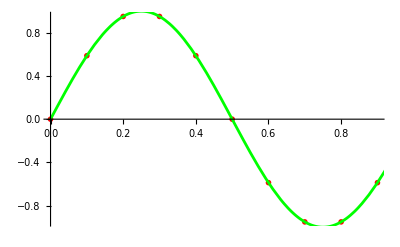

```mathematica
Show[plotnum,plotexact]
```

```mathematica
(*plot normnal*)
```

```mathematica
ys=Import["/Users/michelecastellana/Documents/finite_elements/first_order_pde/periodic/solution/nodal_values/ys.csv"][[2;;]];
u=Import["/Users/michelecastellana/Documents/finite_elements/first_order_pde/periodic/solution/nodal_values/u.csv"][[2;;]]
n=Import["/Users/michelecastellana/Documents/finite_elements/first_order_pde/periodic/solution/nodal_values/n.csv"][[2;;]];
```

{{1.,0.,0,1.,0,0},{0.809017,0.,0,0.9,0,0},{0.309017,0.,0,0.8,0,0},{-0.309017,0.,0,0.7,0,0},{-0.809017,0.,0,0.6,0,0},{-1.,0.,0,0.5,0,0},{-0.809017,0.,0,0.4,0,0},{-0.309017,0.,0,0.3,0,0},{0.309017,0.,0,0.2,0,0},{0.809017,0.,0,0.1,0,0},{1.,0.,0,0.,0,0}}

```mathematica
(*points for the vector field*)
```

```mathematica
X=Table[{ys[[i,1]]+u[[i,1]],ys[[i,2]]+u[[i,2]]},{i,1,Length[u]}]
```

{{2.,1.34397×10^-16},{1.61803,-0.587785},{0.618034,-0.951057},{-0.618034,-0.951057},{-1.61803,-0.587785},{-2.,1.40458×10^-16},{-1.61803,0.587785},{-0.618034,0.951057},{0.618034,0.951057},{1.61803,0.587785},{2.,5.16755×10^-17}}

```mathematica
(*values of the vector field*)
```

```mathematica
V=Table[{n[[i,1]],n[[i,2]]},{i,1,Length[n]}]
```

{{-0.999096,-0.0010665},{-0.567119,0.824307},{-0.160352,0.987084},{0.160352,0.987094},{0.567119,0.824415},{0.999096,4.53485×10^-15},{0.567119,-0.824415},{0.160352,-0.987094},{-0.160352,-0.987084},{-0.567119,-0.824307},{-0.999096,0.0010665}}

```mathematica
data=Table[{X[[i]],V[[i]]},{i,1,Length[X]}]
```

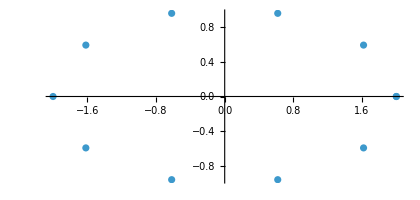

```mathematica
ListPlot[X,AspectRatio->Automatic]
```

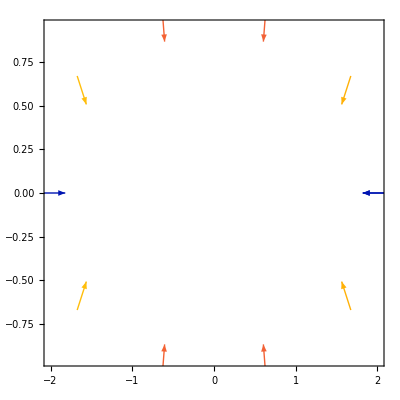

```mathematica
ListVectorPlot[data,VectorPoints->All]
```